# Calculation of p(n) + ϕ -> p(n) +π^0

## Run

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

### S-Channel

```mathematica
SpinorUBar[p4,m].GS[p3].GA[5].(GS[p2]+2m).SpinorU[p1,m]
```

ū(p4,m).(γ̄·OverBar[p3]).(γ̄)^5.(γ̄·OverBar[p2]+2 m).(u(p1,m))

```mathematica
sc = ComplexConjugate[%]
```

-(φ(OverBar[p1],m)).(γ̄·OverBar[p2]+2 m).(γ̄)^5.(γ̄·OverBar[p3]).(φ(OverBar[p4],m))

```mathematica
spart =-(GS[p4]+m).GS[p3].GA[5].(GS[p2]+2m).(GS[p1]+m).(GS[p2]+2m).GA[5].GS[p3]
```

-(γ̄·OverBar[p4]+m).(γ̄·OverBar[p3]).(γ̄)^5.(γ̄·OverBar[p2]+2 m).(γ̄·OverBar[p1]+m).(γ̄·OverBar[p2]+2 m).(γ̄)^5.(γ̄·OverBar[p3])

```mathematica
postTraces = TR[%]
```

-4 (4 m^4 OverBar[p3]^2+4 m^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p2])+4 m^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^2 OverBar[p3]^2 (OverBar[p2]·OverBar[p4])-8 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+m^2 OverBar[p2]^2 OverBar[p3]^2-OverBar[p2]^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])+2 OverBar[p3]^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])+2 OverBar[p2]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4]))

Throw stuff on shell

```mathematica
postTraces =postTraces/. Pair[Momentum[p3],Momentum[p3]]-> mPi^2/.Pair[Momentum[p2],Momentum[p2]]-> mPhi^2/.Pair[Momentum[p1],Momentum[p1]]-> m^2/.Pair[Momentum[p4],Momentum[p4]]-> m^2
```

-4 (4 m^2 mPi^2 (OverBar[p1]·OverBar[p2])+4 m^2 mPi^2 (OverBar[p1]·OverBar[p4])+4 m^2 mPi^2 (OverBar[p2]·OverBar[p4])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-8 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-mPhi^2 mPi^2 (OverBar[p1]·OverBar[p4])+2 mPhi^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+2 mPi^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])-4 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

Replace p1.pj (pCM is CM momentum of incoming particles, pp is CM outgoing momentum)

```mathematica
postTraces =postTraces/. Pair[Momentum[p1],Momentum[p2]]-> Ephi*m/.Pair[Momentum[p1],Momentum[p3]]-> (EpCM*EpiCM-Cos[θ]*pCM*pp)/.Pair[Momentum[p1],Momentum[p4]]-> (EpCM*EppCM +Cos[θ]*pCM*pp)
```

-4 (-8 m^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))+2 mPhi^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))+2 Ephi m mPi^2 (OverBar[p2]·OverBar[p4])-4 Ephi m (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^2 mPi^2 (OverBar[p2]·OverBar[p4])-8 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))+4 Ephi m^3 mPi^2+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

Replace p2.pj and p3.p4

```mathematica
postTraces =postTraces/. Pair[Momentum[p3],Momentum[p4]]-> ((1/2)(mPhi^2 +m^2 -mPi^2-mpp^2+2*Ephi*m))/.Pair[Momentum[p2],Momentum[p3]]-> (EphiCM*EpiCM+Cos[θ]*pCM*pp)/.Pair[Momentum[p2],Momentum[p4]]-> (EphiCM*EppCM -Cos[θ]*pCM*pp)
```

-4 (-4 m^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+mPhi^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-4 m^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ))-2 Ephi m (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ))+2 Ephi m mPi^2 (EphiCM EppCM-pCM pp cos(θ))+4 Ephi m^3 mPi^2+4 m^2 mPi^2 (EphiCM EppCM-pCM pp cos(θ))+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

### T-Channel

```mathematica
tpart =-(GS[p4]+m).(-GS[p2]+2m).GS[p3].GA[5].(GS[p1]+m).GA[5].GS[p3].(-GS[p2]+2m)
```

-(γ̄·OverBar[p4]+m).(2 m-γ̄·OverBar[p2]).(γ̄·OverBar[p3]).(γ̄)^5.(γ̄·OverBar[p1]+m).(γ̄)^5.(γ̄·OverBar[p3]).(2 m-γ̄·OverBar[p2])

```mathematica
postTracet=TR[%]
```

-4 (4 m^4 OverBar[p3]^2+8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])-4 m^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p2])+4 m^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 m^2 OverBar[p3]^2 (OverBar[p2]·OverBar[p4])+m^2 OverBar[p2]^2 OverBar[p3]^2-4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])-OverBar[p2]^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])+2 OverBar[p3]^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])+2 OverBar[p2]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4]))

Throw stuff on-shell

```mathematica
postTracet =postTracet/. Pair[Momentum[p3],Momentum[p3]]-> mPi^2/.Pair[Momentum[p2],Momentum[p2]]-> mPhi^2/.Pair[Momentum[p1],Momentum[p1]]-> m^2/.Pair[Momentum[p4],Momentum[p4]]-> m^2
```

-4 (-4 m^2 mPi^2 (OverBar[p1]·OverBar[p2])+4 m^2 mPi^2 (OverBar[p1]·OverBar[p4])-4 m^2 mPi^2 (OverBar[p2]·OverBar[p4])+8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-mPhi^2 mPi^2 (OverBar[p1]·OverBar[p4])+2 mPhi^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+2 mPi^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])-4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

Replace p1.pj (pCM is CM momentum of incoming particles, pp is CM outgoing momentum)

```mathematica
postTracet =postTracet/. Pair[Momentum[p1],Momentum[p2]]-> Ephi*m/.Pair[Momentum[p1],Momentum[p3]]-> (EpCM*EpiCM-Cos[θ]*pCM*pp)/.Pair[Momentum[p1],Momentum[p4]]-> (EpCM*EppCM +Cos[θ]*pCM*pp)
```

-4 (8 m^2 (OverBar[p2]·OverBar[p3]) (EpCM EpiCM-pCM pp cos(θ))-8 m^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))+2 mPhi^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))-4 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))+2 Ephi m mPi^2 (OverBar[p2]·OverBar[p4])-4 m^2 mPi^2 (OverBar[p2]·OverBar[p4])+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-4 Ephi m^3 mPi^2+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

Replace p2.pj and p3.p4

```mathematica
postTracet =postTracet/. Pair[Momentum[p3],Momentum[p4]]-> ((1/2)(mPhi^2 +m^2 -mPi^2-mpp^2+2*Ephi*m))/.Pair[Momentum[p2],Momentum[p3]]-> (EphiCM*EpiCM+Cos[θ]*pCM*pp)/.Pair[Momentum[p2],Momentum[p4]]-> (EphiCM*EppCM -Cos[θ]*pCM*pp)
```

-4 (-4 m^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+mPhi^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ))+8 m^2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))+2 Ephi m mPi^2 (EphiCM EppCM-pCM pp cos(θ))-4 Ephi m^3 mPi^2-4 m^2 mPi^2 (EphiCM EppCM-pCM pp cos(θ))+4 m^4 mPi^2+m^2 mPhi^2 mPi^2)

### Cross terms

```mathematica
crosspart =-((GS[p4]+m).GS[p3].GA[5].(GS[p2]+2m).(GS[p1]+m).GA[5].GS[p3].(-GS[p2]+2m)+(GS[p4]+m).(-GS[p2]+2m).GS[p3].GA[5].(GS[p1]+m).(GS[p2]+2m).GA[5].GS[p3])
```

-(γ̄·OverBar[p4]+m).(2 m-γ̄·OverBar[p2]).(γ̄·OverBar[p3]).(γ̄)^5.(γ̄·OverBar[p1]+m).(γ̄·OverBar[p2]+2 m).(γ̄)^5.(γ̄·OverBar[p3])-(γ̄·OverBar[p4]+m).(γ̄·OverBar[p3]).(γ̄)^5.(γ̄·OverBar[p2]+2 m).(γ̄·OverBar[p1]+m).(γ̄)^5.(γ̄·OverBar[p3]).(2 m-γ̄·OverBar[p2])

```mathematica
postTracex=TR[%]
```

-8 (2 m^2 (OverBar[p2]·OverBar[p3])^2-2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])^2+4 m^4 OverBar[p3]^2+4 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])+4 m^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-m^2 OverBar[p2]^2 OverBar[p3]^2+2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+OverBar[p2]^2 OverBar[p3]^2 (OverBar[p1]·OverBar[p4])-2 OverBar[p3]^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])-2 OverBar[p2]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4]))

Throw stuff on-shell

```mathematica
postTracex =postTracex/. Pair[Momentum[p3],Momentum[p3]]-> mPi^2/.Pair[Momentum[p2],Momentum[p2]]-> mPhi^2/.Pair[Momentum[p1],Momentum[p1]]-> m^2/.Pair[Momentum[p4],Momentum[p4]]-> m^2
```

-8 (2 m^2 (OverBar[p2]·OverBar[p3])^2-2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])^2+4 m^2 mPi^2 (OverBar[p1]·OverBar[p4])+4 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])-8 m^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+mPhi^2 mPi^2 (OverBar[p1]·OverBar[p4])-2 mPhi^2 (OverBar[p1]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-2 mPi^2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p4])+2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+2 (OverBar[p1]·OverBar[p2]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^4 mPi^2-m^2 mPhi^2 mPi^2)

Replace p1.pj (pCM is CM momentum of incoming particles, pp is CM outgoing momentum)

```mathematica
postTracex =postTracex/. Pair[Momentum[p1],Momentum[p2]]-> Ephi*m/.Pair[Momentum[p1],Momentum[p3]]-> (EpCM*EpiCM-Cos[θ]*pCM*pp)/.Pair[Momentum[p1],Momentum[p4]]-> (EpCM*EppCM +Cos[θ]*pCM*pp)
```

-8 (-2 (OverBar[p2]·OverBar[p3])^2 (EpCM EppCM+pCM pp cos(θ))+2 m^2 (OverBar[p2]·OverBar[p3])^2+4 m^2 (OverBar[p2]·OverBar[p3]) (EpCM EpiCM-pCM pp cos(θ))-8 m^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))-2 mPhi^2 (OverBar[p3]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))+2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (EpCM EpiCM-pCM pp cos(θ))-2 Ephi m mPi^2 (OverBar[p2]·OverBar[p4])+2 Ephi m (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 m^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))+4 m^4 mPi^2-m^2 mPhi^2 mPi^2)

Replace p2.pj and p3.p4

```mathematica
postTracex =postTracex/. Pair[Momentum[p3],Momentum[p4]]-> ((1/2)(mPhi^2 +m^2 -mPi^2-mpp^2+2*Ephi*m))/.Pair[Momentum[p2],Momentum[p3]]-> (EphiCM*EpiCM+Cos[θ]*pCM*pp)/.Pair[Momentum[p2],Momentum[p4]]-> (EphiCM*EppCM -Cos[θ]*pCM*pp)
```

-8 (-4 m^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ))-2 (EpCM EppCM+pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))^2+4 m^2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+4 m^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 m^2 (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ))+Ephi m (2 Ephi m+m^2+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ))-2 Ephi m mPi^2 (EphiCM EppCM-pCM pp cos(θ))+2 m^2 (EphiCM EpiCM+pCM pp cos(θ))^2+4 m^4 mPi^2-m^2 mPhi^2 mPi^2)

### Bring them together

```mathematica
matSq = (1/2)(c^2 * gs^2)*(postTraces/(s-m^2)^2 + postTracet/(t-m^2)^2 +postTracex/((s-m^2)(t-m^2)))
```

1/2 c^2 gs^2 (-1/((s-m^2)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2+4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((t-m^2)^2)4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2+8 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((s-m^2) (t-m^2))8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (EphiCM EpiCM+pCM pp cos(θ))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2-2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 (EphiCM EpiCM+pCM pp cos(θ))^2 (EpCM EppCM+pCM pp cos(θ))))

```mathematica
diffCrossSec = (1/8*Pi)^2 * ((matSq)/(EphiCM+EpCM)^2)*(Abs[pp]/Abs[pCM])
```

1/(128 (EpCM+EphiCM)^2 Abs[pCM])c^2 gs^2 π^2 Abs[pp] (-1/((s-m^2)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2+4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((t-m^2)^2)4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2+8 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((s-m^2) (t-m^2))8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (EphiCM EpiCM+pCM pp cos(θ))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2-2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 (EphiCM EpiCM+pCM pp cos(θ))^2 (EpCM EppCM+pCM pp cos(θ))))

Replace Mandlestam Variables

```mathematica
diffCrossSec = diffCrossSec/. s -> (mPhi^2 +m^2 + 2*Ephi*m) /.t -> (mPi^2 + m^2-2*(EpCM*EpiCM-Cos[θ]*pCM*pp))
```

1/(128 (EpCM+EphiCM)^2 Abs[pCM])c^2 gs^2 π^2 Abs[pp] (-1/((mPhi^2+2 Ephi m)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2+4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((mPi^2-2 (EpCM EpiCM-pCM pp cos(θ)))^2)4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2+8 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-(8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (EphiCM EpiCM+pCM pp cos(θ))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2-2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 (EphiCM EpiCM+pCM pp cos(θ))^2 (EpCM EppCM+pCM pp cos(θ))))/((mPhi^2+2 Ephi m) (mPi^2-2 (EpCM EpiCM-pCM pp cos(θ)))))

```mathematica
unIntCrossSec = 2*Pi*Sin[θ] *diffCrossSec
```

1/(64 (EpCM+EphiCM)^2 Abs[pCM])c^2 gs^2 π^3 Abs[pp] (-1/((mPhi^2+2 Ephi m)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2+4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((mPi^2-2 (EpCM EpiCM-pCM pp cos(θ)))^2)4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2+8 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-(8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (EphiCM EpiCM+pCM pp cos(θ))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2-2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 (EphiCM EpiCM+pCM pp cos(θ))^2 (EpCM EppCM+pCM pp cos(θ))))/((mPhi^2+2 Ephi m) (mPi^2-2 (EpCM EpiCM-pCM pp cos(θ))))) sin(θ)

### Make appropriate replacements

Replace couplings (phi is now scalar mixing of higgs and ϕ)

```mathematica
crossSec2 = unIntCrossSec/. gs -> (ϕ*m*f/v)/.c -> (gA/(2*fPi))
```

1/(256 (EpCM+EphiCM)^2 fPi^2 v^2 Abs[pCM])f^2 gA^2 m^2 π^3 ϕ^2 Abs[pp] (-1/((mPhi^2+2 Ephi m)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2+4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-1/((mPi^2-2 (EpCM EpiCM-pCM pp cos(θ)))^2)4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-4 mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m^2+8 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2+2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))-4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))-mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ)))-(8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (EphiCM EpiCM+pCM pp cos(θ))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ)) m^2+4 mPi^2 (EpCM EppCM+pCM pp cos(θ)) m^2-2 Ephi mPi^2 (EphiCM EppCM-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EphiCM EpiCM+pCM pp cos(θ)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (EpCM EpiCM-pCM pp cos(θ))+2 (EpCM EpiCM-pCM pp cos(θ)) (EphiCM EppCM-pCM pp cos(θ)) (EphiCM EpiCM+pCM pp cos(θ))+mPhi^2 mPi^2 (EpCM EppCM+pCM pp cos(θ))-2 (EphiCM EpiCM+pCM pp cos(θ))^2 (EpCM EppCM+pCM pp cos(θ))))/((mPhi^2+2 Ephi m) (mPi^2-2 (EpCM EpiCM-pCM pp cos(θ))))) sin(θ)

Replace CM variables (get down to just incoming energy of ϕ in the lab frame and particle masses)

```mathematica
crossSec2 = crossSec2/. EphiCM -> Sqrt[mPhi^2 +pCM^2]/.EpCM -> Sqrt[m^2 + pCM^2]/. EpiCM -> Sqrt[mPi^2 +pp^2]/.EppCM -> Sqrt[mpp^2 + pp^2]
```

(f^2 gA^2 m^2 π^3 ϕ^2 Abs[pp] (-1/((mPhi^2+2 Ephi m)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) m^2+4 mPi^2 (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m^2+4 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2)) m^2+2 Ephi mPi^2 (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ))-mPhi^2 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2)))-(4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) m^2-4 mPi^2 (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) m^2+8 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m^2+4 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2)) m^2+2 Ephi mPi^2 (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ))-4 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2))-mPhi^2 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2))))/(mPi^2-2 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)))^2-(8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m^2+4 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m^2+4 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2)) m^2-2 Ephi mPi^2 (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2)) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ))+2 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ)) (√(mPhi^2+pCM^2) √(mpp^2+pp^2)-pCM pp cos(θ)) (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2))+mPhi^2 mPi^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2))-2 (pCM pp cos(θ)+√(mPhi^2+pCM^2) √(mPi^2+pp^2))^2 (pCM pp cos(θ)+√(m^2+pCM^2) √(mpp^2+pp^2))))/((mPhi^2+2 Ephi m) (mPi^2-2 (√(m^2+pCM^2) √(mPi^2+pp^2)-pCM pp cos(θ))))) sin(θ))/(256 fPi^2 (√(m^2+pCM^2)+√(mPhi^2+pCM^2))^2 v^2 Abs[pCM])

```mathematica
crossSec2 = crossSec2/. pp -> ((((mPhi^2 + m^2 -mPi^2 -mpp^2)/2+Ephi*m)^2 - mPi^2 *mpp^2)/(mPi^2 +mpp^2 +2((mPhi^2 + m^2 -mPi^2 -mpp^2)/2+Ephi*m)))/.pCM -> ((Ephi^2*m^2-mPhi^2m^2)/(2*Ephi*m + m^2 + mPhi^2))
```

(f^2 gA^2 m^2 π^3 ϕ^2 Abs[((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)/(mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))] (-1/((mPhi^2+2 Ephi m)^2)4 (4 mPi^2 m^4+4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m^2+4 mPi^2 (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+4 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+2 Ephi mPi^2 (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m-2 Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))))-mPhi^2 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))))-(4 (4 mPi^2 m^4-4 Ephi mPi^2 m^3+mPhi^2 mPi^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m^2-4 mPi^2 (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m^2+8 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+4 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+2 Ephi mPi^2 (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m+mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))))-4 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))-mPhi^2 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))))/(mPi^2-2 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))))^2-(8 (4 mPi^2 m^4-mPhi^2 mPi^2 m^2+2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))^2 m^2-4 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m^2-2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+4 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2+4 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m^2-2 Ephi mPi^2 (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) m+Ephi (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))) m-mPhi^2 (m^2+2 Ephi m+mPhi^2-mPi^2-mpp^2) (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))))+2 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))) (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))+mPhi^2 mPi^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))-2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))^2 (((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))))+√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mpp^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2)))))/((mPhi^2+2 Ephi m) (mPi^2-2 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)) √(mPi^2+(((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2)^2)/((mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))^2))-((Ephi^2 m^2-m^2 mPhi^2) ((Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2))^2-mPi^2 mpp^2) cos(θ))/((m^2+2 Ephi m+mPhi^2) (mPi^2+mpp^2+2 (Ephi m+1/2 (m^2+mPhi^2-mPi^2-mpp^2)))))))) sin(θ))/(256 fPi^2 (√(m^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2))+√(mPhi^2+((Ephi^2 m^2-m^2 mPhi^2)^2)/((m^2+2 Ephi m+mPhi^2)^2)))^2 v^2 Abs[(Ephi^2 m^2-m^2 mPhi^2)/(m^2+2 Ephi m+mPhi^2)])

### Plug in values

```mathematica
m = 0.938;
mPi =0.135;
mpp = 0.938;
f = 0.3;
gA = 1.3;
fPi = 0.130;
v=246;
```

```mathematica
crossSecRep = crossSec2
```

(0.0000158485 ϕ^2 Abs[((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)/(2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)] (-1/((mPhi^2+1.876 Ephi)^2)4 ((mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) mPhi^2-0.018225 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)) mPhi^2+0.0160352 mPhi^2+0.0601639 Ephi-3.51938 (mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))+0.0341901 Ephi (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))+0.0641406 (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))-1.876 Ephi (mPhi^2+1.876 Ephi-0.018225) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))-3.51938 (mPhi^2+1.876 Ephi-0.018225) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))+0.0641406 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844))+0.0564337)-(4 ((mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) mPhi^2-0.018225 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)) mPhi^2+0.0160352 mPhi^2-0.0601639 Ephi-3.51938 (mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))+0.0341901 Ephi (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))-0.0641406 (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))+7.03875 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))-4 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))+0.0641406 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844))+0.0564337))/(0.018225-2 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))))^2-(8 (-(mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) mPhi^2+0.018225 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)) mPhi^2-0.0160352 mPhi^2+1.75969 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))^2-3.51938 (mPhi^2+1.876 Ephi-0.018225) (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))-0.0341901 Ephi (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))+0.938 Ephi (mPhi^2+1.876 Ephi-0.018225) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))-1.75969 (mPhi^2+1.876 Ephi-0.018225) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))+3.51938 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))+2 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))) (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))-2 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225))^2 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844))+0.0641406 (((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069))+√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.879844))+0.0564337))/((mPhi^2+1.876 Ephi) (0.018225-2 (√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844) √((((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352)^2)/((2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)^2)+0.018225)-((0.879844 Ephi^2-0.879844 mPhi^2) ((0.938 Ephi+1/2 (mPhi^2-0.018225))^2-0.0160352) cos(θ))/((mPhi^2+1.876 Ephi+0.879844) (2 (0.938 Ephi+1/2 (mPhi^2-0.018225))+0.898069)))))) sin(θ))/((√(((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)+0.879844)+√(mPhi^2+((0.879844 Ephi^2-0.879844 mPhi^2)^2)/((mPhi^2+1.876 Ephi+0.879844)^2)))^2 Abs[(0.879844 Ephi^2-0.879844 mPhi^2)/(mPhi^2+1.876 Ephi+0.879844)])

```mathematica
(*Integrate[crossSecRep,{θ,0,Pi}] Too hard!*)
```

```mathematica
toIntCS =crossSecRep/.mPhi-> .1 /. Ephi -> 3 /. ϕ-> 0.0005
```

5.21343×10^-13 sin(θ) (-0.125837 (0.166711 (1.86319-1.46708 cos(θ))-19.7219 (1.86575-1.46708 cos(θ))-51.4062 (1.46708 cos(θ)+1.4812)+0.0639584 (1.46708 cos(θ)+2.34692)+0.237086)-1/(0.018225-2 (1.86575-1.46708 cos(θ)))^2 4 (-4 (1.46708 cos(θ)+1.4812) (1.86575-1.46708 cos(θ)) (1.86319-1.46708 cos(θ))+0.0384297 (1.86319-1.46708 cos(θ))-19.7219 (1.86575-1.46708 cos(θ))+7.03875 (1.46708 cos(θ)+1.4812) (1.86575-1.46708 cos(θ))+0.0639584 (1.46708 cos(θ)+2.34692)-0.123898)-1/(0.018225-2 (1.86575-1.46708 cos(θ)))1.41894 (2 (1.46708 cos(θ)+1.4812) (1.86319-1.46708 cos(θ)) (1.86575-1.46708 cos(θ))+3.51938 (1.46708 cos(θ)+1.4812) (1.86575-1.46708 cos(θ))-0.10257 (1.86319-1.46708 cos(θ))-19.8343 (1.86575-1.46708 cos(θ))-2 (1.46708 cos(θ)+2.34692) (1.46708 cos(θ)+1.4812)^2+1.75969 (1.46708 cos(θ)+1.4812)^2+5.925 (1.46708 cos(θ)+1.4812)+0.0643229 (1.46708 cos(θ)+2.34692)+0.0562734))

```mathematica
crossSection = Integrate[toIntCS,{θ,0,Pi}]
```

1.18848×10^-11

### Convert to appropriate units and determine penetration distance

```mathematica
numberDensity = 5*10^28;
```

1 GeV^-2 = 0.389 mb

```mathematica
crossSectionB = crossSection * 0.389*10^(-3)*10^(-28) (*In m^2*)
```

4.62319×10^-43

```mathematica
meanFreePath = 1/(crossSectionB*numberDensity)
```

4.32602×10^13

```mathematica
BeamStrength = Exp[-l/meanFreePath]
```

ⅇ^(-2.31159×10^-14 l)

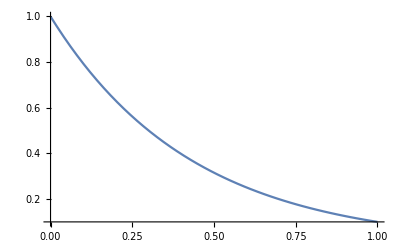

```mathematica
Plot[BeamStrength,{l,0,10^14}]
```